good video: https://www.youtube.com/watch?v=g7zFl8EnbzI

```mathematica
bimg=-Graphics-;
fimg=-Graphics-;
mimg=-Graphics-;
```

```mathematica
ImageAdd[ImageMultiply[fimg,mimg],ImageMultiply[bimg,ColorNegate[mimg]]]
```

-Graphics-

```mathematica
cfimg=ColorConvert[fimg,"GrayScale"];
cbimg=ColorConvert[bimg,"GrayScale"];
```

```mathematica
n=100;
fimgData=ImageData[rfimg=ImageResize[cfimg,{n,n}]];
bimgData=ImageData[rbimg=ImageResize[cbimg,{n,n}]];
mimgData=Unitize[ImageData[rmimg=Image[ImageResize[mimg,{n,n}],"Bit"]]];
```

```mathematica
g[x_,y_]:=If[mimgData[[x,y]]==0,bimgData[[x,y]],fimgData[[x,y]]]
```

```mathematica
Image[Table[g[x,y],{x,1,n},{y,1,n}]]
```

-Graphics-

```mathematica
PrependTo[$Path,NotebookDirectory[]];
<<poisson.m
{A,b}=constructMatricies[rfimg,rbimg,rmimg];
```

```mathematica
PixelValue[LaplacianFilter[rfimg,1],{50,50}]
```

-0.137086

```mathematica
x=LeastSquares[A,b,Method->"Krylov"];
```

```mathematica
ImageAdd[rbimg,Image[Reverse@Partition[Normal[x],n]]]
```

-Graphics-

```mathematica
Dimensions[b]
```

{10000}

```mathematica
Dimensions[A]
```

{10000,10000}

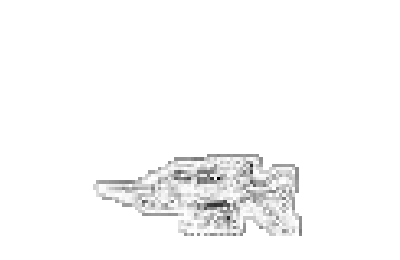

```mathematica
Partition[x,n]//ArrayPlot
```

```mathematica
ClearAll[x]
```

```mathematica
LinearSolve[A,b,Method->{"Krylov",Method->"ConjugateGradient"}]
```

LinearSolve::kryzrow: Each row of the sparse matrix SparseArray[Automatic, {6581, 6581}, 0.`, {« 1 »}] must contain at least one nonzero element.

LinearSolve[SparseArray[<1131>, {6581, 6581}],SparseArray[<1131>, {6581}],Method→{Krylov,Method→ConjugateGradient}]

```mathematica
res=FindMinimum[Norm[A.k-b],{k,ConstantArray[0,Times@@Dimensions[A]]}];
```

Dot::dotsh: Tensors SparseArray[Automatic, {6581, 6581}, 0, {« 1 »}] and {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 43309511 »} have incompatible shapes.

$Aborted

```mathematica
A//Dimensions
```

{6581,6581}

```mathematica
Dimensions[b]
```

{6581}

```mathematica
LeastSquares
```

```mathematica
A={{1,1},{1,2},{1,3}};
b={7,7,8};
```

```mathematica
FindMinimum[Norm[A.k-b],{k,ConstantArray[0,Last@Dimensions[A]]}]
```

FindMinimum::nrnum: The function value {12.7279, 12.7279, 12.7279} is not a real number at {k} = {{0., 0.}}.

FindMinimum[Norm[A.k-b],{k,ConstantArray[0,Last[Dimensions[A]]]}]

```mathematica
Norm[A.ConstantArray[0,Last@Dimensions[A]]-b]
```

9 √2

```mathematica
vars=Table[ToExpression["v"<>ToString[i]],{i,1,Last[Dimensions[A]]}];
```

```mathematica
Length[vars]
```

6581

```mathematica
FindMinimum[Norm[A.vars-b],vars]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.34364×10^-7,{v1→1.,v2→1.,v3→1.,v4→1.,v5→1.,v6→1.,v7→1.,v8→1.,v9→1.,6564,v6574→-1.23426,v6575→-1.20433,v6576→-1.10339,v6577→-1.14013,v6578→-1.25304,v6579→-1.15458,v6580→-1.21568,v6581→-1.88235}}
 |  |  |  |